https://arxiv.org/pdf/1307.6925.pdf controlla

```mathematica
subtract[x_]:=HeavisideTheta[x]HeavisideTheta[1-x]alpha/2/Pi(
-2(1-x)/x+2m2overq2max x +(1+(1-x)^2)/x Log[(1-x)/x^2/m2overq2max]
)
```

```mathematica
beta=alpha/Pi (Log[1/m2overq2max]-1)
```

(alpha (-1+Log[1/m2overq2max]))/π

```mathematica
PDFmu[x_]:=HeavisideTheta[x]HeavisideTheta[1-x]Exp[-EulerGamma beta+3/4 beta]/(Gamma[1+beta])beta(1-x)^(beta-1)
```

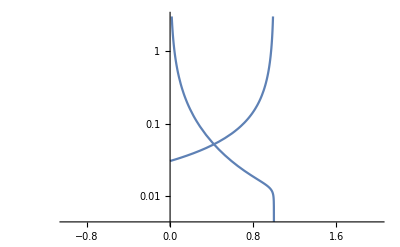

```mathematica
LogPlot[{subtract[x],PDFmu[x]}/.{alpha->1/137,m2overq2max->(0.1/100)^2},{x,-1,2}]
```

```mathematica
subtract[1/2]/.{alpha->1/137,m2overq2max->(0.1/1000)^2}
```

0.0531886

```mathematica
Convolve[DiracDelta[x],subtract[x],x,y]
```

(alpha HeavisideTheta[1-y,y] (2 (-1+y+m2overq2max y^2)+(2-2 y+y^2) Log[(1-y)/(m2overq2max y^2)]))/(2 π y)

```mathematica
Convolve[PDFmu[x],subtract[x],x,y]
```

```mathematica
Integrate[DiracDelta[x-y]subtract[x],{x,0,1},Assumptions->1>=y>=0]
Integrate[DiracDelta[x]subtract[x-y],{x,0,1},Assumptions->1>=y>=0]
```

(alpha HeavisideTheta[1-y,y] (2 (-1+y+m2overq2max y^2)+(2+(-2+y) y) Log[(1-y)/(m2overq2max y^2)]))/(2 π y)

-(alpha HeavisideTheta[0] (-2-2 y+2 m2overq2max y^2+(2+2 y+y^2) Log[(1+y)/(m2overq2max y^2)]))/(2 π y)

```mathematica
convoluted[y_]:=NIntegrate[Simplify[ PDFmu[x]  subtract[x-y]]/.{alpha->1/137,m2overq2max->(0.1/1000)^2},{x,0,1}]
```

```mathematica
NIntegrate[ PDFmu[x]  subtract[x-y]/.{alpha->1/137,m2overq2max->(0.1/1000)^2,y->0.9999},{x,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.999862239331173224669326027314042448779218830168247222900390625}. NIntegrate obtained 495.547 and 163.106 for the integral and error estimates.

495.547

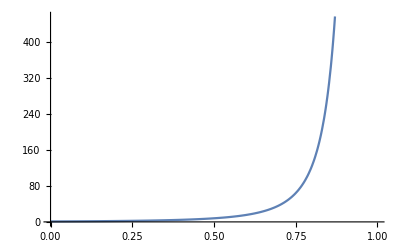

```mathematica
Plot[(1-x)^(-3),{x,0,1}]
```

```mathematica
beta=alpha/Pi (Log[1/m2overq2max]-1)
```

(alpha (-1+Log[1/m2overq2max]))/π

```mathematica
PDFmu[x_]:=Exp[-EulerGamma beta+3/4 beta]/(Gamma[1+beta])beta(1-x)^(beta-1)
```

```mathematica
subtract[1/2]/.{alpha->1/137,m2overq2max->(0.1/1000)^2}
```

0.0531886

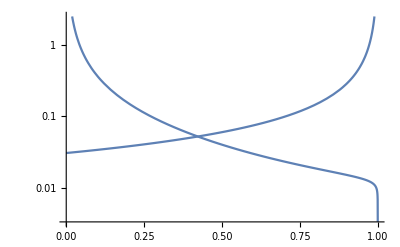

```mathematica
LogPlot[{subtract[x],PDFmu[x]}/.{alpha->1/137,m2overq2max->(0.1/100)^2},{x,0,1}]
```

```mathematica
PDFmu[0.2]/.{alpha->1/137,m2overq2max->(0.1/100)^2}
```

0.0377813

```mathematica
convoluted[0.2]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.201156}. NIntegrate obtained -0.00195626 and 0.0189546 for the integral and error estimates.

-0.00195626

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0000332834}. NIntegrate obtained 0.0362736 and 0.0151498 for the integral and error estimates.

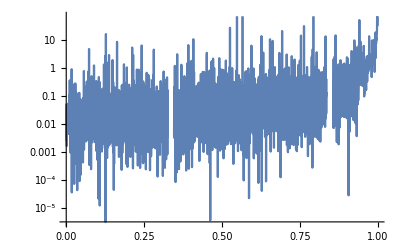

```mathematica
LogPlot[convoluted[x],{x,0,1}]
```

```mathematica
sumtractMellin=Integrate[Simplify[(subtract[x]x^(s-1))(*/.{alpha->1/137,m2overq2max->(0.1/100)^2}*)],{x,0,Infinity}]
```

ConditionalExpression[(alpha (-2+s+2 (6+m2overq2max) s^2+(5-2 m2overq2max) s^3-2 m2overq2max s^4+2 m2overq2max s^5+(-1+s) s (1+s) (2+s+s^2) Log[1/m2overq2max]-(-1+s) s (1+s) (2+s+s^2) (EulerGamma+PolyGamma[0,s])))/(2 π s^2 (-1+s^2)^2), Re[s]>1]

```mathematica
PDFmuMellin=Integrate[(PDFmu[x] x^(s-1)),{x,0,Infinity}]
```

ConditionalExpression[(alpha ⅇ^(-(alpha (-3+4 EulerGamma) (-1+Log[1/m2overq2max]))/(4 π)) Gamma[s] Gamma[(alpha (-1+Log[1/m2overq2max]))/π] (-1+Log[1/m2overq2max]))/(π Gamma[1+(alpha (-1+Log[1/m2overq2max]))/π] Gamma[(-alpha+π s+alpha Log[1/m2overq2max])/π]), Re[alpha-alpha Log[1/m2overq2max]]<0&&Re[alpha (1+Log[m2overq2max])]<0&&Re[s]>0]

```mathematica
mellinconvresult=FullSimplify[sumtractMellin PDFmuMellin,Assumptions->{Re[alpha (1+Log[m2overq2max])]<0,Re[alpha]<Re[alpha Log[1/m2overq2max]], s>1}]
```

(alpha ⅇ^(-(alpha (-3+4 EulerGamma) (-1+Log[1/m2overq2max]))/(4 π)) Gamma[s] (-2+s+2 (6+m2overq2max) s^2+(5-2 m2overq2max) s^3-2 m2overq2max s^4+2 m2overq2max s^5+(-1+s) s (1+s) (2+s+s^2) Log[1/m2overq2max]-(-1+s) s (1+s) (2+s+s^2) (EulerGamma+PolyGamma[0,s])))/(2 π s^2 (-1+s^2)^2 Gamma[(-alpha+π s+alpha Log[1/m2overq2max])/π])

```mathematica
mellinconv[t_]:=Evaluate[mellinconvresult]/.s->t
```

```mathematica
FullSimplify[mellinconv[s], Assumptions->s>1]
```

(alpha ⅇ^(-(alpha (-3+4 EulerGamma) (-1+Log[1/m2overq2max]))/(4 π)) Gamma[s] (-2+s+2 (6+m2overq2max) s^2+(5-2 m2overq2max) s^3-2 m2overq2max s^4+2 m2overq2max s^5+(-1+s) s (1+s) (2+s+s^2) Log[1/m2overq2max]-(-1+s) s (1+s) (2+s+s^2) (EulerGamma+PolyGamma[0,s])))/(2 π s^2 (-1+s^2)^2 Gamma[(-alpha+π s+alpha Log[1/m2overq2max])/π])

```mathematica
Integrate[(x^(-(2+I z))mellinconv[2+I z])/.{alpha->1/137,m2overq2max->(0.1/1000)^2},{z,-Infinity,Infinity}]
```

$Aborted

```mathematica
Im[x^(-(2+I z))mellinconv[2+I z]/.{alpha->1/137,m2overq2max->(0.1/1000)^2}]
```

0.00116987 Im[(x^(-2-ⅈ z) Gamma[2+ⅈ z] (12. (2+ⅈ z)^2+5. (2+ⅈ z)^3-2.×10^-8 (2+ⅈ z)^4+2.×10^-8 (2+ⅈ z)^5+18.4207 (1+ⅈ z) (2+ⅈ z) (3+ⅈ z) (4+(2+ⅈ z)^2+ⅈ z)+ⅈ z-(1+ⅈ z) (2+ⅈ z) (3+ⅈ z) (4+(2+ⅈ z)^2+ⅈ z) (EulerGamma+PolyGamma[0,2+ⅈ z])))/((-1+(2+ⅈ z)^2)^2 (2+ⅈ z)^2 Gamma[(0.127158+π (2+ⅈ z))/π])]